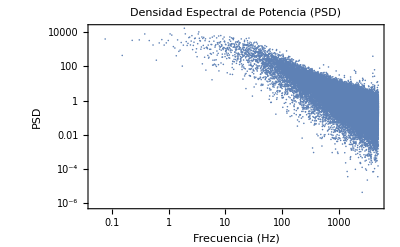

El valor estimado de beta es: 1.45817

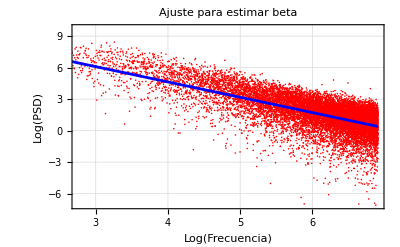

```mathematica
(*Cargar los datos del archivo*)
data=Import["/Users/keniajuayerk/Desktop/k_channel.txt","Table"];

(*Extraer los tiempos y valores*)
time=data[[All,1]];
values=data[[All,2]];

(*Calcular la longitud de los datos*)
n=Length[values];

(*Calcular el período de muestreo (asumiendo intervalos regulares)*)
samplingPeriod=time[[2]]-time[[1]];

(*Calcular la frecuencia de muestreo*)
samplingFrequency=1/samplingPeriod;

(*Calcular la transformada de Fourier*)
fourier=Fourier[values,FourierParameters->{1,-1}];

(*Calcular la PSD*)
psd=Abs[fourier]^2/n;

(*Crear las frecuencias correspondientes*)
frequencies=Table[(i-1)*samplingFrequency/n,{i,n}];

(*Graficar la PSD en escala logarítmica*)
ListLogLogPlot[Transpose[{frequencies[[1;;Floor[n/2]]],psd[[1;;Floor[n/2]]]}],PlotRange->All,Frame->True,FrameLabel->{"Frecuencia (Hz)","PSD"},PlotLabel->"Densidad Espectral de Potencia (PSD)",GridLines->Automatic]

(*Ajustar una ley de potencia a la PSD para estimar beta*)
(*Consideramos solo las frecuencias bajas para el ajuste*)
lowFreqRange=Floor[n/10]; (*Ajustar este valor según sea necesario*)

(*Preparar los datos para el ajuste*)
fitData=Transpose[{Log[frequencies[[2;;lowFreqRange]]],Log[psd[[2;;lowFreqRange]]]}];

(*Realizar el ajuste lineal*)
fit=LinearModelFit[fitData,x,x];

(*Extraer la pendiente (beta)*)
beta=-fit["BestFitParameters"][[2]];

(*Mostrar el valor de beta*)
Print["El valor estimado de beta es: ",beta]

(*Graficar el ajuste*)
Show[ListPlot[fitData,PlotStyle->Red,PlotLabel->"Ajuste para estimar beta"],Plot[fit[x],{x,Min[fitData[[All,1]]],Max[fitData[[All,1]]]},PlotStyle->Blue],Frame->True,FrameLabel->{"Log(Frecuencia)","Log(PSD)"},GridLines->Automatic]
```